# ROBOT PARALELO 3RRR PROGRAMA 3. APROXIMACIÓN A LA CINEMÁTICA DIRECTA POR MTH Y SIMULACIÓN POR CINEMÁTICA INVERSA MÉTODO NUMÉRICO.

Se obtienen las ecuaciones de cinemática directa a partir de la tabla de Denavit-Hartenberg, así como se validan utilizando el método numérico de Newton Raphson.

## FUNCIONES

```mathematica
(*FUNCIONES DE Matrices de Rotación 3x3 PARA CUALQUIER VARIABLE *)
Rx[α_]:={{1,0,0},{0,Cos[α], -Sin[α]}, {0,Sin[α], Cos[α]}};   
Ry[ϕ_]:={{Cos[ϕ],0,Sin[ϕ]},{0,1,0}, {-Sin[ϕ],0,Cos[ϕ]}};  
Rz[θ_]:={{Cos[θ], -Sin[θ],0},{Sin[θ], Cos[θ],0},{0,0,1}};
(*FUNCIONES de Matrices HOMEGENEAS de Traslación y Rotación 4x4 PARA CUALQUIER VARIABLE *)
Tx[x_]:={{1,0,0,x},{0,1,0,0},{0,0,1,0},{0,0,0,1}}
Ty[y_]:={{1,0,0,0},{0,1,0,y},{0,0,1,0},{0,0,0,1}}
Tz[z_]:={{1,0,0,0},{0,1,0,0},{0,0,1,z},{0,0,0,1}}
Txyz[x_,y_,z_]:=Tx[x].Ty[y].Tz[z]
Qx[α_]:={{1,0,0,0},{0,Cos[α], -Sin[α], 0},{0, Sin[α], Cos[α],0},{0,0,0,1}}
Qy[ϕ_]:={{Cos[ϕ], 0, Sin[ϕ],0},{0,1,0,0},{-Sin[ϕ],0,Cos[ϕ],0},{0,0,0,1}}
Qz[θ_]:={{Cos[θ], -Sin[θ],0,0},{Sin[θ], Cos[θ],0,0},{0,0,1,0},{0,0,0,1}}
(*FUNCIONES de Matrices HOMEGENEAS De Denavit-Hartenberg *)
Q[θ_, d_, a_, α_]:=Qz[θ].Tz[d].Tx[a].Qx[α]
Ma=Q[θ1, d1, a1, α1];
Ma//MatrixForm
(*FUNCIONES ADICIONALES *)
n={0,0,0,1};
T3D[P_]:={P⟦1⟧,P⟦2⟧,P⟦3⟧ }
M3D[Q_]:={{Q⟦1,1⟧,Q⟦1,2⟧, Q⟦1,3⟧ },{Q⟦2,1⟧,Q⟦2,2⟧, Q⟦2,3⟧},{Q⟦3,1⟧,Q⟦3,2⟧, Q⟦3,3⟧}}
T={{NX, OX, AX},{NY, OY, AY},{NZ, OZ, AZ}};
T//MatrixForm
(*Función para la evolución de las variables articulares*)
Grafica[tabla_, rojo_,verde_,azul_,EjeX_,EjeY_]:=ListPlot[tabla,ImageSize->300, Joined->True, PlotStyle->{AbsoluteThickness[6], RGBColor[rojo,verde,azul]},BaseStyle->{14,FontFamily->"Arial"}, Frame->True, FrameLabel->{EjeX,EjeY},GridLines->Automatic, PlotRange->All];
```

(Cos[θ1] | -Cos[α1] Sin[θ1] | Sin[α1] Sin[θ1] | a1 Cos[θ1]
Sin[θ1] | Cos[α1] Cos[θ1] | -Cos[θ1] Sin[α1] | a1 Sin[θ1]
0 | Sin[α1] | Cos[α1] | d1
0 | 0 | 0 | 1)

(NX | OX | AX
NY | OY | AY
NZ | OZ | AZ)

## CINEMÁTICA DIRECTA 5 GDL DENAVIT-HARTENBERG

## MTH7- OBTENER LAS MATRICES ^(i-1)A_i

```mathematica
(*Cadena 1 *)
Underoverscript[a, 11, 0]=Qz[θ11].Tx[ℓ11];
Underoverscript[a, 12, 11]=Qz[θ12].Tx[ℓ12];
Underoverscript[a, 13, 12]=Qz[θ13].Tx[ℓ13];
(*Cadena 2*)
Underoverscript[a, 20, 0]=Txyz[ℓx2,ℓy2,0];
Underoverscript[a, 21, 20]=Qz[θ21].Tx[ℓ21];
Underoverscript[a, 22, 21]=Qz[θ22].Tx[ℓ22];
Underoverscript[a, 23, 22]=Qz[θ23].Tx[ℓ23];
(*Cadena 3*)
Underoverscript[a, 30, 0]=Txyz[ℓx3,ℓy3,0];
Underoverscript[a, 31, 30]=Qz[θ31].Tx[ℓ31];
Underoverscript[a, 32, 31]=Qz[θ32].Tx[ℓ32];
Underoverscript[a, 33, 32]=Qz[θ33].Tx[ℓ33];
```

## MTH8- OBTENER LAS MATRICES ^0 A_5=^0 A_1.^1 A_2.^2 A_3.....

```mathematica
(*Cadena 1*)
Underoverscript[a, 12, 0]=Underoverscript[a, 11, 0].Underoverscript[a, 12, 11]//Simplify;
Underoverscript[a, 13, 0]=Underoverscript[a, 11, 0].Underoverscript[a, 12, 11].Underoverscript[a, 13, 12]//Simplify;
Underoverscript[a, 13, 0].n//MatrixForm

(*Cadena 2*)
Underoverscript[a, 21, 0]=Underoverscript[a, 20, 0].Underoverscript[a, 21, 20]//Simplify;
Underoverscript[a, 22, 0]=Underoverscript[a, 20, 0].Underoverscript[a, 21, 20].Underoverscript[a, 22, 21]//Simplify;
Underoverscript[a, 23, 0]=Underoverscript[a, 20, 0].Underoverscript[a, 21, 20].Underoverscript[a, 22, 21].Underoverscript[a, 23, 22]//Simplify;
Underoverscript[a, 23, 0].n//MatrixForm

(*Cadena 3*)
Underoverscript[a, 31, 0]=Underoverscript[a, 30, 0].Underoverscript[a, 31, 30]//Simplify;
Underoverscript[a, 32, 0]=Underoverscript[a, 30, 0].Underoverscript[a, 31, 30].Underoverscript[a, 32, 31]//Simplify;
Underoverscript[a, 33, 0]=Underoverscript[a, 30, 0].Underoverscript[a, 31, 30].Underoverscript[a, 32, 31].Underoverscript[a, 33, 32]//Simplify;
Underoverscript[a, 33, 0].n//MatrixForm
```

(ℓ11 Cos[θ11]+ℓ12 Cos[θ11+θ12]+ℓ13 Cos[θ11+θ12+θ13]
ℓ11 Sin[θ11]+ℓ12 Sin[θ11+θ12]+ℓ13 Sin[θ11+θ12+θ13]
0
1)

(ℓx2+ℓ21 Cos[θ21]+ℓ22 Cos[θ21+θ22]+ℓ23 Cos[θ21+θ22+θ23]
ℓy2+ℓ21 Sin[θ21]+ℓ22 Sin[θ21+θ22]+ℓ23 Sin[θ21+θ22+θ23]
0
1)

(ℓx3+ℓ31 Cos[θ31]+ℓ32 Cos[θ31+θ32]+ℓ33 Cos[θ31+θ32+θ33]
ℓy3+ℓ31 Sin[θ31]+ℓ32 Sin[θ31+θ32]+ℓ33 Sin[θ31+θ32+θ33]
0
1)

## MTH9- Vector de Posición del Efector Final y SubMatriz de Orientación

### Vector de Posición

```mathematica
(*CADENA 1 *)
X1=Underoverscript[a, 13, 0]⟦1,4⟧//Simplify
Y1=Underoverscript[a, 13, 0]⟦2,4⟧//Simplify
Z1=Underoverscript[a, 13, 0]⟦3,4⟧//Simplify;
Φ1=θ11+θ12+θ13-30°

(*CADENA 2*)
X2=Underoverscript[a, 23, 0]⟦1,4⟧//Simplify
Y2=Underoverscript[a, 23, 0]⟦2,4⟧//Simplify
Z2=Underoverscript[a, 23, 0]⟦3,4⟧//Simplify;
Φ2=θ21+θ22+θ23-150°

(*CADENA 3*)
X3=Underoverscript[a, 33, 0]⟦1,4⟧//Simplify
Y3=Underoverscript[a, 33, 0]⟦2,4⟧//Simplify
Z3=Underoverscript[a, 33, 0]⟦3,4⟧//Simplify;
Φ3=θ31+θ32+θ33-270°
```

ℓ11 Cos[θ11]+ℓ12 Cos[θ11+θ12]+ℓ13 Cos[θ11+θ12+θ13]

ℓ11 Sin[θ11]+ℓ12 Sin[θ11+θ12]+ℓ13 Sin[θ11+θ12+θ13]

-30 °+θ11+θ12+θ13

ℓx2+ℓ21 Cos[θ21]+ℓ22 Cos[θ21+θ22]+ℓ23 Cos[θ21+θ22+θ23]

ℓy2+ℓ21 Sin[θ21]+ℓ22 Sin[θ21+θ22]+ℓ23 Sin[θ21+θ22+θ23]

-150 °+θ21+θ22+θ23

ℓx3+ℓ31 Cos[θ31]+ℓ32 Cos[θ31+θ32]+ℓ33 Cos[θ31+θ32+θ33]

ℓy3+ℓ31 Sin[θ31]+ℓ32 Sin[θ31+θ32]+ℓ33 Sin[θ31+θ32+θ33]

-270 °+θ31+θ32+θ33

### SubMatriz de Rotación (ORIENTACIÓN DEL EFECTOR FINAL)

```mathematica
(*CADENA 1*)
NX1=Underoverscript[a, 13, 0]⟦1,1⟧//FullSimplify;
OX1=Underoverscript[a, 13, 0]⟦1,2⟧//FullSimplify;
AX1=Underoverscript[a, 13, 0]⟦1,3⟧//FullSimplify;

NY1=Underoverscript[a, 13, 0]⟦2,1⟧//FullSimplify;
OY1=Underoverscript[a, 13, 0]⟦2,2⟧//FullSimplify;
AY1=Underoverscript[a, 13, 0]⟦2,3⟧//FullSimplify;

NZ1=Underoverscript[a, 13, 0]⟦3,1⟧//FullSimplify;
OZ1=Underoverscript[a, 13, 0]⟦3,2⟧//FullSimplify;
AZ1=Underoverscript[a, 13, 0]⟦3,3⟧//FullSimplify;
(*CADENA 2*)
NX2=Underoverscript[a, 23, 0]⟦1,1⟧//FullSimplify;
OX2=Underoverscript[a, 23, 0]⟦1,2⟧//FullSimplify;
AX2=Underoverscript[a, 23, 0]⟦1,3⟧//FullSimplify;

NY2=Underoverscript[a, 23, 0]⟦2,1⟧//FullSimplify;
OY2=Underoverscript[a, 23, 0]⟦2,2⟧//FullSimplify;
AY2=Underoverscript[a, 23, 0]⟦2,3⟧//FullSimplify;

NZ2=Underoverscript[a, 23, 0]⟦3,1⟧//FullSimplify;
OZ2=Underoverscript[a, 23, 0]⟦3,2⟧//FullSimplify;
AZ2=Underoverscript[a, 23, 0]⟦3,3⟧//FullSimplify;

(*CADENA 3*)
NX3=Underoverscript[a, 33, 0]⟦1,1⟧//FullSimplify;
OX3=Underoverscript[a, 33, 0]⟦1,2⟧//FullSimplify;
AX3=Underoverscript[a, 33, 0]⟦1,3⟧//FullSimplify;

NY3=Underoverscript[a, 33, 0]⟦2,1⟧//FullSimplify;
OY3=Underoverscript[a, 33, 0]⟦2,2⟧//FullSimplify;
AY3=Underoverscript[a, 33, 0]⟦2,3⟧//FullSimplify;

NZ3=Underoverscript[a, 33, 0]⟦3,1⟧//FullSimplify;
OZ3=Underoverscript[a, 33, 0]⟦3,2⟧//FullSimplify;
AZ3=Underoverscript[a, 33, 0]⟦3,3⟧//FullSimplify;
```

## CINEMÁTICA IVERSA DE FORMA CERRADA MÉTODO ALGEBRICO.

### CADENA 1

#### THETA 12

```mathematica
(*CADENA1*)
X1cv=X1/.θ11+θ12+θ13->ϕ+30°;
Y1cv=Y1/.θ11+θ12+θ13->ϕ+30°;
X1LD=X1cv-ℓ13 Cos[30 °+ϕ];
Y1LD=Y1cv-ℓ13 Sin[30 °+ϕ];
X1LI=x-ℓ13 Cos[30 °+ϕ];
Y1LI=y-ℓ13 Sin[30 °+ϕ];
SumLDxyc=X1LD^2+Y1LD^2//FullSimplify;
SumLIxyc=X1LI^2+Y1LI^2//FullSimplify;
SolC12=Solve[SumLDxyc==SumLIxyc,Cos[θ12] ]//Flatten;
C12=Cos[θ12]/.SolC12;
S12=√(1-C12^2);
t12=ArcTan[C12,S12]
```

ArcTan[(x^2+y^2-ℓ11^2-ℓ12^2-2 x ℓ13 Cos[30 °+ϕ]+ℓ13^2 Cos[30 °+ϕ]^2-2 y ℓ13 Sin[30 °+ϕ]+ℓ13^2 Sin[30 °+ϕ]^2)/(2 ℓ11 ℓ12),√(1-((x^2+y^2-ℓ11^2-ℓ12^2-2 x ℓ13 Cos[30 °+ϕ]+ℓ13^2 Cos[30 °+ϕ]^2-2 y ℓ13 Sin[30 °+ϕ]+ℓ13^2 Sin[30 °+ϕ]^2)^2)/(4 ℓ11^2 ℓ12^2))]

#### SOLUCIÓN THETA 11

```mathematica
X1cvE=X1cv//TrigExpand;
Y1cvE=Y1cv//TrigExpand;
SOLC11S11=Solve[{X1cvE==x, Y1cvE==y},{Cos[θ11],Sin[θ11]}]//Flatten//FullSimplify;
C11=Cos[θ11]/.SOLC11S11⟦1⟧;
S11=Sin[θ11]/.SOLC11S11⟦2⟧;
t11=ArcTan[C11, S11]
```

ArcTan[(2 x ℓ12 Cos[θ12]-ℓ12 (√3 ℓ13 Cos[θ12-ϕ]-2 y Sin[θ12]+ℓ13 Sin[θ12-ϕ])+ℓ11 (2 x-√3 ℓ13 Cos[ϕ]+ℓ13 Sin[ϕ]))/(2 (ℓ11^2+ℓ12^2+2 ℓ11 ℓ12 Cos[θ12])),(2 y ℓ11+2 y ℓ12 Cos[θ12]-2 x ℓ12 Sin[θ12]-ℓ13 (ℓ12 Cos[θ12-ϕ]+ℓ11 Cos[ϕ]+√3 (-ℓ12 Sin[θ12-ϕ]+ℓ11 Sin[ϕ])))/(2 (ℓ11^2+ℓ12^2+2 ℓ11 ℓ12 Cos[θ12]))]

### CADENA 2

#### THETA 22

```mathematica
(*CADENA2*)
X2cv=X2/.θ21+θ22+θ23->ϕ+150°;
Y2cv=Y2/.θ21+θ22+θ23->ϕ+150°;
X2LD=X2cv-ℓ23 Cos[150 °+ϕ]-ℓx2;
Y2LD=Y2cv-ℓ23 Sin[150 °+ϕ]-ℓy2;
X2LI=x-ℓ23 Cos[150 °+ϕ]-ℓx2;
Y2LI=y-ℓ23 Sin[150 °+ϕ]-ℓy2;
Sum2LDxyc=X2LD^2+Y2LD^2//FullSimplify;
Sum2LIxyc=X2LI^2+Y2LI^2//FullSimplify;
SolC22=Solve[Sum2LDxyc==Sum2LIxyc,Cos[θ22] ]//Flatten;
C22=Cos[θ22]/.SolC22;
S22=√(1-C22^2);
t22=ArcTan[C22,S22]
```

ArcTan[(-ℓ21^2-ℓ22^2+(x-ℓx2+ℓ23 Cos[30 °-ϕ])^2+(-y+ℓy2+ℓ23 Sin[30 °-ϕ])^2)/(2 ℓ21 ℓ22),√(1-((-ℓ21^2-ℓ22^2+(x-ℓx2+ℓ23 Cos[30 °-ϕ])^2+(-y+ℓy2+ℓ23 Sin[30 °-ϕ])^2)^2)/(4 ℓ21^2 ℓ22^2))]

#### SOLUCIÓN THETA 21

```mathematica
X2cvE=X2cv//TrigExpand;
Y2cvE=Y2cv//TrigExpand;
SOLC21S21=Solve[{X2cvE==x, Y2cvE==y},{Cos[θ21],Sin[θ21]}]//Flatten//FullSimplify;
C21=Cos[θ21]/.SOLC21S21⟦1⟧;
S21=Sin[θ21]/.SOLC21S21⟦2⟧;
t21=ArcTan[C21, S21]
```

ArcTan[(2 ℓ21 (x-ℓx2)+2 ℓ22 (x-ℓx2) Cos[θ22]+√3 ℓ22 ℓ23 Cos[θ22-ϕ]+2 ℓ22 (y-ℓy2) Sin[θ22]-ℓ22 ℓ23 Sin[θ22-ϕ]+ℓ21 ℓ23 (√3 Cos[ϕ]+Sin[ϕ]))/(2 (ℓ21^2+ℓ22^2+2 ℓ21 ℓ22 Cos[θ22])),(2 ℓ21 (y-ℓy2)+2 ℓ22 (y-ℓy2) Cos[θ22]+2 ℓ22 (-x+ℓx2) Sin[θ22]-ℓ23 (ℓ22 Cos[θ22-ϕ]+ℓ21 Cos[ϕ]+√3 (ℓ22 Sin[θ22-ϕ]-ℓ21 Sin[ϕ])))/(2 (ℓ21^2+ℓ22^2+2 ℓ21 ℓ22 Cos[θ22]))]

### CADENA 3

#### THETA 32

```mathematica
(*CADENA2*)
X3cv=X3/.θ31+θ32+θ33->ϕ+270°;
Y3cv=Y3/.θ31+θ32+θ33->ϕ+270°;
X3LD=X3cv-ℓ33 Cos[270 °+ϕ]-ℓx3;
Y3LD=Y3cv-ℓ33 Sin[270 °+ϕ]-ℓy3;
X3LI=x-ℓ33 Cos[270 °+ϕ]-ℓx3;
Y3LI=y-ℓ33 Sin[270 °+ϕ]-ℓy3;
Sum3LDxyc=X3LD^2+Y3LD^2//FullSimplify;
Sum3LIxyc=X3LI^2+Y3LI^2//FullSimplify;
SolC32=Solve[Sum3LDxyc==Sum3LIxyc,Cos[θ32] ]//Flatten;
C32=Cos[θ32]/.SolC32;
S32=√(1-C32^2);
t32=ArcTan[C32,S32]
```

ArcTan[(-ℓ31^2-ℓ32^2+(y-ℓy3+ℓ33 Cos[ϕ])^2+(-x+ℓx3+ℓ33 Sin[ϕ])^2)/(2 ℓ31 ℓ32),√(1-((-ℓ31^2-ℓ32^2+(y-ℓy3+ℓ33 Cos[ϕ])^2+(-x+ℓx3+ℓ33 Sin[ϕ])^2)^2)/(4 ℓ31^2 ℓ32^2))]

#### SOLUCIÓN THETA 21

```mathematica
X3cvE=X3cv//TrigExpand;
Y3cvE=Y3cv//TrigExpand;
SOLC31S31=Solve[{X3cvE==x, Y3cvE==y},{Cos[θ31],Sin[θ31]}]//Flatten//FullSimplify;
C31=Cos[θ31]/.SOLC31S31⟦1⟧;
S31=Sin[θ31]/.SOLC31S31⟦2⟧;
t31=ArcTan[C31, S31]
```

ArcTan[(x ℓ31-ℓ31 ℓx3+ℓ32 (x-ℓx3) Cos[θ32]+ℓ32 (y-ℓy3) Sin[θ32]+ℓ32 ℓ33 Sin[θ32-ϕ]-ℓ31 ℓ33 Sin[ϕ])/(ℓ31^2+ℓ32^2+2 ℓ31 ℓ32 Cos[θ32]),(ℓ32 (y-ℓy3) Cos[θ32]+ℓ32 ℓ33 Cos[θ32-ϕ]+ℓ31 (y-ℓy3+ℓ33 Cos[ϕ])+ℓ32 (-x+ℓx3) Sin[θ32])/(ℓ31^2+ℓ32^2+2 ℓ31 ℓ32 Cos[θ32])]

### DATOS

```mathematica
ℓ11=30;
ℓ12=40;
ℓ13=15;

ℓ21=30;
ℓ22=40;
ℓ23=15;
ℓ31=30;
ℓ32=40;
ℓ33=15;
ℓx2=60;
ℓy2=0;
ℓx3=30;
ℓy3=60;
ϕ=10°;
tf=100;
aa=4;
Cero={0,0,0};
For[t=0, t≤tf, t+=1,
Perfil=10*(t/tf)^3-15*(t/tf)^4 +6*(t/tf)^5;Trayectoria[t]={
2*aa*Cos[2*Pi*Perfil]-aa*Cos[4*Pi*Perfil]+30,
2*aa*Sin[4*Pi*Perfil]-aa*Sin[4*Pi*Perfil]+30,
0
}
];
Tablaxyz=Table[{Trayectoria[t]⟦1⟧,Trayectoria[t]⟦2⟧,Trayectoria[t]⟦3⟧},{t,0,tf,1}];
TrayectoriaEF=Line[Tablaxyz];
Graphics3D[
{
{AbsoluteThickness[1],RGBColor[1,0,0],TrayectoriaEF}
},
Axes->True, AxesLabel->{x,y,z},AxesStyle->{Red, Green, Blue}, BaseStyle->{24, FontFamily["Arial"]}, ImageSize->300, PlotRange->{{-45,40}, {-40,40},{-0,1}}
]
```

-Graphics3D-

## Valores de las variables articulares CI

```mathematica
For[t=0, t≤tf, t+=1,
x=Trayectoria[t]⟦1⟧;
y=Trayectoria[t]⟦2⟧;
z=Trayectoria[t]⟦3⟧;
(*CADENA1*)
θ12a[t]=t12;
θ12=θ12a[t];

θ11a[t]=t11;
θ11=θ11a[t];

(*CADENA2*)
θ22a[t]=t22;
θ22=θ22a[t];

θ21a[t]=t21;
θ21=θ21a[t];

(*CADENA3*)
θ32a[t]=t32;
θ32=θ32a[t];

θ31a[t]=t31;
θ31=θ31a[t];
]
θ12a[40]//N
θ11a[60]//N 
θ22a[40]//N
θ21a[60]//N 
θ32a[40]//N
θ31a[60]//N
```

2.4704

-0.559497

2.3866

0.716995

2.68795

2.09096

## SIMULACIÓN

```mathematica
Animate[
θ12=θ12a[t];
θ11=θ11a[t];
θ22=θ22a[t];
θ21=θ21a[t];
θ32=θ32a[t];
θ31=θ31a[t];
θ13=ϕ+30°-θ11-θ12;
θ23=ϕ+150°-θ21-θ22;
θ33=ϕ+270°-θ31-θ32;

(*Cadena 1*)
Eslabon11=Line[{Cero,T3D[Underoverscript[a, 11, 0].n]}];
Eslabon12=Line[{T3D[Underoverscript[a, 11, 0].n],T3D[Underoverscript[a, 12, 0].n]}];
Eslabon13=Line[{T3D[Underoverscript[a, 12, 0].n],T3D[Underoverscript[a, 13, 0].n]}];
(*Cadena 2*)
Eslabon20=Line[{Cero,T3D[Underoverscript[a, 20, 0].n]}];
Eslabon21=Line[{T3D[Underoverscript[a, 20, 0].n],T3D[Underoverscript[a, 21, 0].n]}];
Eslabon22=Line[{T3D[Underoverscript[a, 21, 0].n],T3D[Underoverscript[a, 22, 0].n]}];
Eslabon23=Line[{T3D[Underoverscript[a, 22, 0].n],T3D[Underoverscript[a, 23, 0].n]}];

(*Cadena 3*)
Eslabon30=Line[{Cero,T3D[Underoverscript[a, 30, 0].n]}];
Eslabon31=Line[{T3D[Underoverscript[a, 30, 0].n],T3D[Underoverscript[a, 31, 0].n]}];
Eslabon32=Line[{T3D[Underoverscript[a, 31, 0].n],T3D[Underoverscript[a, 32, 0].n]}];
Eslabon33=Line[{T3D[Underoverscript[a, 32, 0].n],T3D[Underoverscript[a, 33, 0].n]}];
(*Plataforma móvil *)
Eslabon1222=Line[{T3D[Underoverscript[a, 12, 0].n],T3D[Underoverscript[a, 22, 0].n]}];
Eslabon1232=Line[{T3D[Underoverscript[a, 12, 0].n],T3D[Underoverscript[a, 32, 0].n]}];
Eslabon2232=Line[{T3D[Underoverscript[a, 22, 0].n],T3D[Underoverscript[a, 32, 0].n]}];

Graphics3D[
{
{AbsoluteThickness[1],RGBColor[1,0,0],TrayectoriaEF}, 
(*cadena 1*)
{AbsoluteThickness[5],RGBColor[1,0,0.5],Eslabon11}, 
{AbsoluteThickness[4],RGBColor[1,0.7,0],Eslabon12}, 
{AbsoluteThickness[3],RGBColor[1,1,0.5],Eslabon13},
(*cadena 2*)
{AbsoluteThickness[.5],RGBColor[1,1,0.5],Eslabon20}, 
{AbsoluteThickness[5],RGBColor[1,0,0.5],Eslabon21}, 
{AbsoluteThickness[4],RGBColor[1,0.7,0],Eslabon22}, 
{AbsoluteThickness[3],RGBColor[1,1,0.5],Eslabon23},

(*cadena 3*)
{AbsoluteThickness[.5],RGBColor[1,1,0.5],Eslabon30}, 
{AbsoluteThickness[5],RGBColor[1,0,0.5],Eslabon31}, 
{AbsoluteThickness[4],RGBColor[1,0.7,0],Eslabon32}, 
{AbsoluteThickness[3],RGBColor[1,1,0.5],Eslabon33},

(*Plataforma móvil*)
{AbsoluteThickness[3],RGBColor[0,1,0],Eslabon1222},
{AbsoluteThickness[3],RGBColor[0,1,0],Eslabon1232},
{AbsoluteThickness[3],RGBColor[0,1,0],Eslabon2232}

},
Axes->True, AxesLabel->{x,y,z},AxesStyle->{Red, Green, Blue}, BaseStyle->{24, FontFamily["Arial"]}, ImageSize->600, PlotRange->{{-100,180}, {-150,180},{-1,1}}
],{t,0,tf,1}
]
```

## EVOLUCIÓN DE LAS VARIABLES ARTICULARES

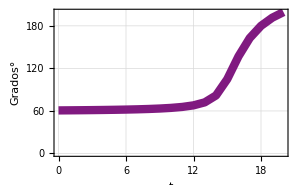

```mathematica
Tabla1=Table[{t, (θ1/.VartArt[t])/Degree},{t,0,tf,1}];
Theta1=Grafica[Tabla1,.5,.1,.5,"t", "Grados°"]
```

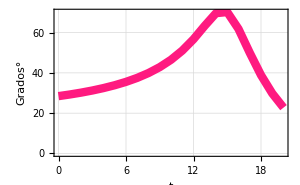

```mathematica
Tabla2=Table[{t, (θ2/.VartArt[t])/Degree},{t,0,tf,1}];
Theta2=Grafica[Tabla2,1,.1,.5,"t", "Grados°"]
```

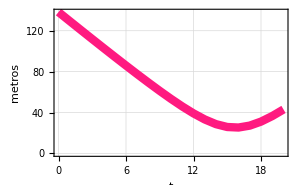

```mathematica
Tabla3=Table[{t, (d3/.VartArt[t])},{t,0,tf,1}];
Theta3=Grafica[Tabla3,1,.1,.5,"t", "metros"]
```

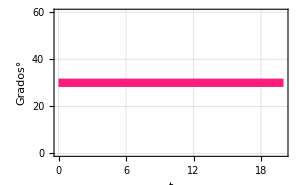

```mathematica
Tabla4=Table[{t, (θ4/.VartArt[t])/Degree},{t,0,tf,1}];
Theta4=Grafica[Tabla4,1,.1,.5,"t", "Grados°"]
```

```mathematica
Tabla5=Table[{t, (θ5/.VartArt[t])/Degree},{t,0,tf,1}];
Theta5=Grafica[Tabla5,1,.1,.5,"t", "Grados°"]
```

-Graphics-

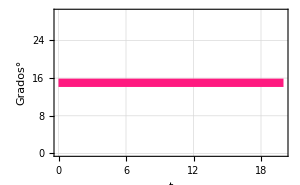

```mathematica
Tabla6=Table[{t, (θ6/.VartArt[t])/Degree},{t,0,tf,1}];
Theta6=Grafica[Tabla6,1,.1,.5,"t", "Grados°"]
```